```mathematica
Phi1[x_Integer]:=Piecewise[{{(1/8)(5-2*I),Abs[x]==0},{(1/8)*(2+I),Abs[x]==1}, {(-1/16),Abs[x]==2}}]
```

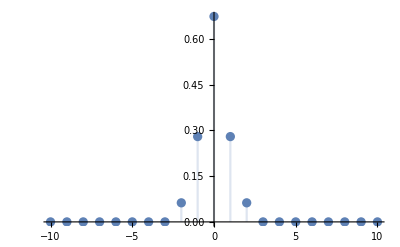

```mathematica
DiscretePlot[Abs[Phi1[x]],{x,-10,10},PlotRange-> All]
```

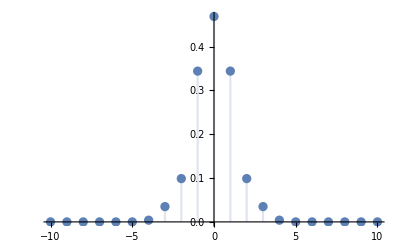

```mathematica
Phi2[x_Integer]:=Sum[Phi1[x-y]*Phi1[y],{y,-2,2}];
DiscretePlot[Abs[Phi2[x]],{x,-10,10},PlotRange-> All]
```

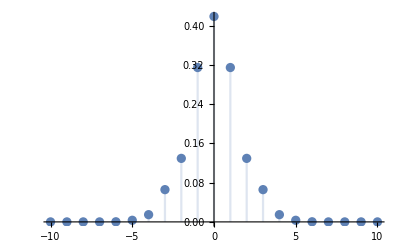

```mathematica
Phi3[x_Integer]:=Sum[Phi2[x-y]*Phi1[y],{y,-2,2}];
DiscretePlot[Abs[Phi3[x]],{x,-10,10},PlotRange-> All]
```

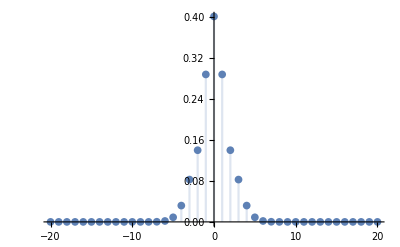

```mathematica
Phi4[x_Integer]:=Sum[Phi3[x-y]*Phi1[y],{y,-2,2}];
DiscretePlot[Abs[Phi4[x]],{x,-20,20},PlotRange-> All]
```

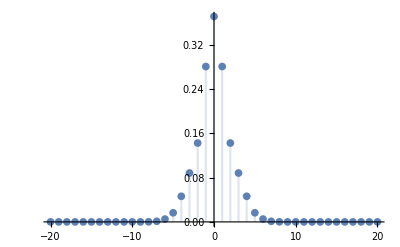

```mathematica
Phi5[x_Integer]:=Sum[Phi4[x-y]*Phi1[y],{y,-2,2}];
DiscretePlot[Abs[Phi5[x]],{x,-20,20},PlotRange-> All]
```

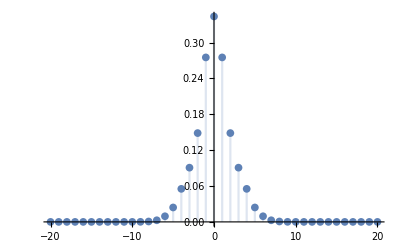

```mathematica
Phi6[x_Integer]:=Sum[Phi5[x-y]*Phi1[y],{y,-2,2}];
DiscretePlot[Abs[Phi6[x]],{x,-20,20},PlotRange-> All]
```

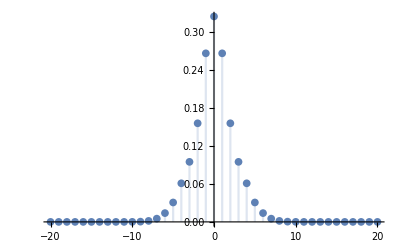

```mathematica
Phi7[x_Integer]:=Sum[Phi6[x-y]*Phi1[y],{y,-2,2}];
DiscretePlot[Abs[Phi7[x]],{x,-20,20},PlotRange-> All]
```

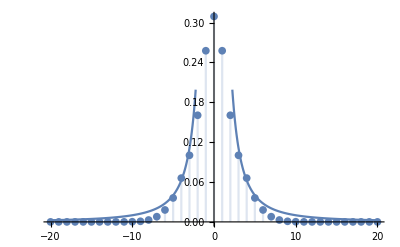

```mathematica
Phi8[x_Integer]:=Sum[Phi7[x-y]*Phi1[y],{y,-2,2}];
Show[DiscretePlot[Abs[Phi8[x]],{x,-20,20},PlotRange-> All],Plot[1/x^2,{x,-20,20}]]
```

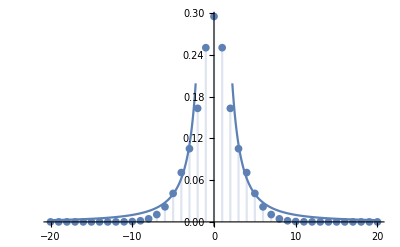

```mathematica
Phi9[x_Integer]:=Sum[Phi8[x-y]*Phi1[y],{y,-2,2}];
Show[DiscretePlot[Abs[Phi9[x]],{x,-20,20},PlotRange-> All],Plot[1/x^2,{x,-20,20}]]
```

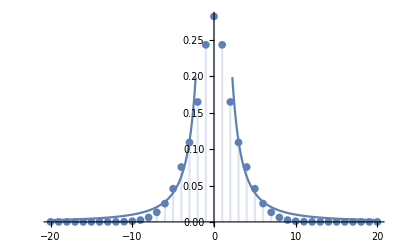

```mathematica
Phi10[x_Integer]:=Sum[Phi9[x-y]*Phi1[y],{y,-2,2}];
Show[DiscretePlot[Abs[Phi10[x]],{x,-20,20},PlotRange-> All],Plot[1/x^2,{x,-20,20}]]
```

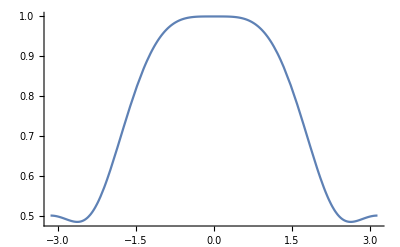

```mathematica
Plot[Abs[(1/8)*(5-2*I)+(1/4)(2+I)*Cos[x] - (1/8)*Cos[2*x]],{x,-Pi,Pi}]
```

```mathematica
FPhi1[x_Integer] := Fourier[[-1/16, (1/8)*(2+I),(1/8)(5-2*I), (1/8)*(2+I) ,-1/16]]
```

```mathematica
Taylor[x_]:=Series[Log[(1/8)(5-2*I) + (1/4)(2+I)*Cos[x] - (1/8)*Cos[2*x]],{x,0,10}]
```

```mathematica
Taylor[x]
```

-(ⅈ x^2)/8-(7/128-ⅈ/96) x^4+(7/768-(173 ⅈ)/23040) x^6-(141/81920-(1159 ⅈ)/645120) x^8+(833/2211840-(269987 ⅈ)/464486400) x^10+O[x]^11

```mathematica
PhiFT[e_,x_]:= (1/(11+Sqrt[3]))*(4-2*Cos[2*e]+(5+Sqrt[3])*Cos[e]+2*(Cos[x]+Sin[x])+(2*Sqrt[3]-2)Cos[e]*Sin[x])
```

```mathematica
Gam[e_,x_]:=Log[PhiFT[e,x+Pi/3]]
```

```mathematica
Simplify[Series[Gam[e,x],{e,0,4},{x,0,2}]]
```

(-(2 x^2)/(11+√3)+O[x]^3)+(1/118 (7-6 √3) x+1/236 (18-7 √3) x^2+O[x]^3) e^2+(-1/(11+√3)+((-7+6 √3) x)/1416+(5 (-15+2 √3) x^2)/(24 (11+√3)^2)+O[x]^3) e^4+O[e]^5

```mathematica
Simplify[PhiFT[0,Pi/3]]
```

1

```mathematica
Simplify[4-2+(5+Sqrt[3])+2(Cos[Pi/3] - Sin[Pi/3]) + (2*Sqrt[3]+2)*Cos[0]*Sin[Pi/3]]
```

11+√3

Claim: adding a skew-symmetric matrix to a working E yields another E. I want to verify/maybe find counter examples?

First example: This is take from the paper.

```mathematica
P[e_,x_]:=(1/(22+2*Sqrt[3]))*(2*e^4 + (Sqrt[3]-1)*e^2*x+4x^2)
```

```mathematica
P[e,x]
```

(2 e^4+(-1+√3) e^2 x+4 x^2)/(22+2 √3)

This defines an E that works.

```mathematica
Em :={{1/4,0},{0,1/2}}
```

```mathematica
MatrixExp[Log[t]*Em]
```

{{t^(1/4),0},{0,√t}}

```mathematica
Simplify[P[e *t^(1/4),√t* x]]
```

(t (2 e^4+(-1+√3) e^2 x+4 x^2))/(2 (11+√3))

```mathematica
t*P[e,x]
```

(t (2 e^4+(-1+√3) e^2 x+4 x^2))/(22+2 √3)

```mathematica
Simplify[P[e t^(1/4),√t x]-t*P[e,x]]
```

0

This defines a skew-symmetric O. O+E gives a new matrix. Verify that O+E is another E that works.

```mathematica
Om := {{0,-1/8},{1/8,0}}
```

```mathematica
Em+Om
```

{{1/4,-1/8},{1/8,1/2}}

```mathematica
Eigenvalues[Em+Om]
```

{3/8,3/8}

```mathematica
MatrixExp[Log[t]*(Em+Om)].{{a},{b}}
```

{{a t^(3/8) (1-Log[t]/8)-1/8 b t^(3/8) Log[t]},{b t^(3/8) (1+Log[t]/8)+1/8 a t^(3/8) Log[t]}}

```mathematica
a t^(3/8) (1-Log[t]/8)-1/8 b t^(3/8) Log[t]//InputForm
```

a*t^(3/8)*(1 - Log[t]/8) - (b*t^(3/8)*Log[t])/8

```mathematica
b t^(3/8) (1+Log[t]/8)+1/8 a t^(3/8) Log[t]//InputForm
```

b*t^(3/8)*(1 + Log[t]/8) + (a*t^(3/8)*Log[t])/8

```mathematica
Simplify[t*P[e,x]-P[a*t^(3/8)*(1-Log[t]/8)-(b*t^(3/8)*Log[t])/8,b*t^(3/8)*(1+Log[t]/8)+(a*t^(3/8)*Log[t])/8]]
```

1/(2 (11+√3))(t (2 e^4+(-1+√3) e^2 x+4 x^2)-(t^(3/2) (-8 a+(a+b) Log[t])^4)/2048-1/512 (-1+√3) t^(9/8) (-8 a+(a+b) Log[t])^2 (8 b+(a+b) Log[t])-1/16 t^(3/4) (8 b+(a+b) Log[t])^2)

Here is another example. This P[ξ] is much simpler and more ``symmetric.’’

```mathematica
PP[a_,b_]:=a^2 + b^2
```

```mathematica
PP[a,b]
```

a^2+b^2

```mathematica
EM:={{1/2,0},{0,1/2}}
```

```mathematica
OM :={{0,-1},{1,0}}
```

```mathematica
MatrixExp[Log[t]*EM]
```

{{√t,0},{0,√t}}

```mathematica
Simplify[MatrixExp[Log[t]*(EM+OM)]]//MatrixForm
```

(√t Cos[Log[t]] | -√t Sin[Log[t]]
√t Sin[Log[t]] | √t Cos[Log[t]])

```mathematica
Simplify[t*PP[a,b] - PP[a*Sqrt[t],b*Sqrt[t]]]
```

0

```mathematica
EM+OM//MatrixForm
```

(1/2 | -1
1 | 1/2)

```mathematica
Eigenvalues[EM+OM]
```

{1/2+ⅈ,1/2-ⅈ}

```mathematica
Simplify[MatrixExp[Log[t]*(EM+OM)]].{{a},{b}}
```

{{a √t Cos[Log[t]]-b √t Sin[Log[t]]},{b √t Cos[Log[t]]+a √t Sin[Log[t]]}}

```mathematica
a √t Cos[Log[t]]-b √t Sin[Log[t]]//InputForm
```

a*Sqrt[t]*Cos[Log[t]] - b*Sqrt[t]*Sin[Log[t]]

```mathematica
b √t Cos[Log[t]]+a √t Sin[Log[t]]//InputForm
```

b*Sqrt[t]*Cos[Log[t]] + a*Sqrt[t]*Sin[Log[t]]

```mathematica
Simplify[t*PP[a,b]-PP[a*Sqrt[t]*Cos[Log[t]]-b*Sqrt[t]*Sin[Log[t]], b*Sqrt[t]*Cos[Log[t]]+a*Sqrt[t]*Sin[Log[t]]]]
```

0

With this particular OM, OM+EM works. What about a different OM?

```mathematica
OM1:={{0,-1/2},{1/2,0}}
```

```mathematica
EM+OM1//MatrixForm
```

(1/2 | -1/2
1/2 | 1/2)

```mathematica
Eigenvalues[EM+OM1]
```

{1/2+ⅈ/2,1/2-ⅈ/2}

```mathematica
Simplify[MatrixExp[Log[t]*(EM+OM1)]].{{a},{b}}
```

{{a √t Cos[Log[t]/2]-b √t Sin[Log[t]/2]},{b √t Cos[Log[t]/2]+a √t Sin[Log[t]/2]}}

```mathematica
a √t Cos[Log[t]/2]-b √t Sin[Log[t]/2]//InputForm
```

a*Sqrt[t]*Cos[Log[t]/2] - b*Sqrt[t]*Sin[Log[t]/2]

```mathematica
b √t Cos[Log[t]/2]+a √t Sin[Log[t]/2]//InputForm
```

b*Sqrt[t]*Cos[Log[t]/2] + a*Sqrt[t]*Sin[Log[t]/2]

```mathematica
Simplify[t*PP[a,b]-PP[a*Sqrt[t]*Cos[Log[t]/2]-b*Sqrt[t]*Sin[Log[t]/2], b*Sqrt[t]*Cos[Log[t]/2]+a*Sqrt[t]*Sin[Log[t]/2]]]
```

0

This also works. So what determines when things work??? Let’s try another wild OM2. Pretty sure this will work as well.

```mathematica
OM2:={{0,-2},{2,0}}
```

```mathematica
EM+OM2//MatrixForm
```

(1/2 | -2
2 | 1/2)

```mathematica
Eigenvalues[EM+OM2]
```

{1/2+2 ⅈ,1/2-2 ⅈ}

```mathematica
Simplify[MatrixExp[Log[t]*(EM+OM2)]].{{a},{b}}
```

{{a √t Cos[2 Log[t]]-b √t Sin[2 Log[t]]},{b √t Cos[2 Log[t]]+a √t Sin[2 Log[t]]}}

```mathematica
a √t Cos[2 Log[t]]-b √t Sin[2 Log[t]]//InputForm
```

a*Sqrt[t]*Cos[2*Log[t]] - b*Sqrt[t]*Sin[2*Log[t]]

```mathematica
b √t Cos[2 Log[t]]+a √t Sin[2 Log[t]]//InputForm
```

b*Sqrt[t]*Cos[2*Log[t]] + a*Sqrt[t]*Sin[2*Log[t]]

```mathematica
Simplify[t*PP[a,b]-PP[a*Sqrt[t]*Cos[2*Log[t]]-b*Sqrt[t]*Sin[2*Log[t]], b*Sqrt[t]*Cos[2*Log[t]]+a*Sqrt[t]*Sin[2*Log[t]]]]
```

0

Conclusion: Looks like Exp()^(2m) = (1/2m)I + O where O is skew-symmetric. Are we guaranteed this everytime?

```mathematica
O2:={{0,-z},{z,0}}
```

```mathematica
Eigenvalues[EM+O2]
```

{1/2 ⅈ (-ⅈ+2 z),-1/2 ⅈ (ⅈ+2 z)}

```mathematica
Simplify[MatrixExp[Log[t]*(EM+O2)]].{{a},{b}}
```

{{a √t Cos[z Log[t]]-b √t Sin[z Log[t]]},{b √t Cos[z Log[t]]+a √t Sin[z Log[t]]}}

```mathematica
Simplify[MatrixExp[Log[t]*(EM+O2)]].{{a},{b}}//InputForm
```

{{a*Sqrt[t]*Cos[z*Log[t]] - b*Sqrt[t]*Sin[z*Log[t]]}, {b*Sqrt[t]*Cos[z*Log[t]] + a*Sqrt[t]*Sin[z*Log[t]]}}

```mathematica
Simplify[t*PP[a,b]-PP[a*Sqrt[t]*Cos[z*Log[t]]-b*Sqrt[t]*Sin[z*Log[t]], b*Sqrt[t]*Cos[z*Log[t]]+a*Sqrt[t]*Sin[z*Log[t]]]]
```

0

So it is definitely the case here that Exp()^(2m) = (1/2m)I + O where O is skew-symmetric. However, this might not generalize to higher dimensions. Let’s consider 3d next.

```mathematica
{{1,0},{0,2}}.{{a,b},{c,d}}
```

{{a,b},{2 c,2 d}}

```mathematica
{{a,b},{c,d}}.{{1,0},{0,2}}
```

{{a,2 b},{c,2 d}}

How about 3d?

```mathematica
P2d[a_,b_]:=a^4+h*a^2*b^2 +b^4
```

```mathematica
E2d:={{1/4,0},{0,1/4}}
```

```mathematica
E2d//MatrixForm
```

(1/4 | 0
0 | 1/4)

Verify that this E3d works:

```mathematica
MatrixExp[Log[x]*E2d]//MatrixForm
```

(x^(1/4) | 0
0 | x^(1/4))

```mathematica
Simplify[x*P2d[a,b]-P2d[a*x^(1/4),b*x^(1/4)]]
```

0

```mathematica
OO:={{0,-z},{z,0}}
```

```mathematica
OO//MatrixForm
```

(0 | -z
z | 0)

```mathematica
MatrixExp[OO*Log[x]].{{a},{b}}
```

{{a Cos[z Log[x]]-b Sin[z Log[x]]},{b Cos[z Log[x]]+a Sin[z Log[x]]}}

Verify that P(a,b) = P(t^OO . (x,y)) here because we’re just taking E = [0].

```mathematica
Simplify[P2d[a,b] - P2d[a Cos[z Log[x]]-b Sin[z Log[x]], b Cos[z Log[x]]+a Sin[z Log[x]]]]
```

-1/4 (-2+h) Sin[2 z Log[x]] (4 a b (a^2-b^2) Cos[2 z Log[x]]+(a^4-6 a^2 b^2+b^4) Sin[2 z Log[x]])

Of course this works, by inspection. But what if we perturb this E by a skew-symmetric O3d?

```mathematica
O2d := {{0,-z},{z,0}}
```

```mathematica
O3d//MatrixForm
```

(0 | -1/4
1/4 | 0)

```mathematica
E3d//MatrixForm
```

(1/4 | 0 | 0
0 | 1/4 | 0
0 | 0 | 1/4)

```mathematica
E3d
```

{{1/4,0,0},{0,1/4,0},{0,0,1/4}}

```mathematica
O3d
```

{{0,-1/4},{1/4,0}}

```mathematica
E2d+O3d//MatrixForm
```

(1/4 | -1/4
1/4 | 1/4)

```mathematica
E2d+O3d
```

{{1/4,-1/4},{1/4,1/4}}

```mathematica
Eigenvalues[E2d+O3d]
```

{1/4+ⅈ/4,1/4-ⅈ/4}

```mathematica
MatrixExp[Log[t]*(E2d+O3d)].{{a},{b}}//InputForm
```

{{a*t^(1/4)*Cos[Log[t]/4] - b*t^(1/4)*Sin[Log[t]/4]}, 
 {b*t^(1/4)*Cos[Log[t]/4] + a*t^(1/4)*Sin[Log[t]/4]}}

```mathematica
Simplify[t*P2d[a,b]-P2d[a*t^(1/4)*Cos[Log[t]/4]-b*t^(1/4)*Sin[Log[t]/4],b*t^(1/4)*Cos[Log[t]/4]+a*t^(1/4)*Sin[Log[t]/4]]]
```

1/2 t Sin[Log[t]/2] (4 a b (a^2-b^2) Cos[Log[t]/2]+(a^4-6 a^2 b^2+b^4) Sin[Log[t]/2])

Does not vanish. What does this say? We clearly see that all a,b,c have the same orders. But it turns out that this particular E3d+O3d does not work. How about a different O3d such that spec(E3d+O3d) is real? Is this possible?

```mathematica
Mat:={{a,-b,-c},{b,a,-d},{c,d,a}}
```

```mathematica
Eigenvalues[Mat]
```

{a,a-√(-b^2-c^2-d^2),a+√(-b^2-c^2-d^2)}

The spectrum of E3d+O3d is real iff d=c=b=0 i.e. O3d is zero. So it is not possible to get E3d+O3d to have real spectrum unless O3d=[0]. But is there a different O3d that works? I doubt this. Let’s try working with a general anti-sym matrix.

```mathematica
O3 := {{0,-m,-n},{m,0,-o},{n,o,0}}
```

```mathematica
E3d+O3
```

{{1/4,-m,-n},{m,1/4,-o},{n,o,1/4}}

```mathematica
Eigenvalues[E3d+O3]
```

{1/4,1/4 (1-4 √(-m^2-n^2-o^2)),1/4 (1+4 √(-m^2-n^2-o^2))}

```mathematica
MatrixExp[Log[t]*(E3d+O3)].{{a},{b},{c}}
```

{{a ((o^2 t^(1/4))/(m^2+n^2+o^2)+((m^2+n^2) t^(1/4-√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2))+((m^2+n^2) t^(1/4+√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2)))+b (-(n o t^(1/4))/(m^2+n^2+o^2)+((n o-m √(-m^2-n^2-o^2)) t^(1/4-√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2))+((n o+m √(-m^2-n^2-o^2)) t^(1/4+√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2)))+c ((m o t^(1/4))/(m^2+n^2+o^2)-((m o+n √(-m^2-n^2-o^2)) t^(1/4-√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2))-((m o-n √(-m^2-n^2-o^2)) t^(1/4+√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2)))},{b ((n^2 t^(1/4))/(m^2+n^2+o^2)+((m^2+o^2) t^(1/4-√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2))+((m^2+o^2) t^(1/4+√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2)))+a (-(n o t^(1/4))/(m^2+n^2+o^2)+((n o+m √(-m^2-n^2-o^2)) t^(1/4-√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2))+((n o-m √(-m^2-n^2-o^2)) t^(1/4+√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2)))+c (-(m n t^(1/4))/(m^2+n^2+o^2)+((m n-o √(-m^2-n^2-o^2)) t^(1/4-√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2))+((m n+o √(-m^2-n^2-o^2)) t^(1/4+√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2)))},{c ((m^2 t^(1/4))/(m^2+n^2+o^2)+((n^2+o^2) t^(1/4-√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2))+((n^2+o^2) t^(1/4+√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2)))+a ((m o t^(1/4))/(m^2+n^2+o^2)-((m o-n √(-m^2-n^2-o^2)) t^(1/4-√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2))-((m o+n √(-m^2-n^2-o^2)) t^(1/4+√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2)))+b (-(m n t^(1/4))/(m^2+n^2+o^2)+((m n+o √(-m^2-n^2-o^2)) t^(1/4-√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2))+((m n-o √(-m^2-n^2-o^2)) t^(1/4+√(-m^2-n^2-o^2)))/(2 (m^2+n^2+o^2)))}}

```mathematica
MatrixExp[Log[t]*(E3d+O3)].{{a},{b},{c}}//InputForm
```

{{a*((o^2*t^(1/4))/(m^2 + n^2 + o^2) + ((m^2 + n^2)*t^(1/4 - Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)) + 
     ((m^2 + n^2)*t^(1/4 + Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2))) + 
   b*(-((n*o*t^(1/4))/(m^2 + n^2 + o^2)) + ((n*o - m*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 - Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)) + 
     ((n*o + m*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 + Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2))) + 
   c*((m*o*t^(1/4))/(m^2 + n^2 + o^2) - ((m*o + n*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 - Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)) - 
     ((m*o - n*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 + Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)))}, 
 {b*((n^2*t^(1/4))/(m^2 + n^2 + o^2) + ((m^2 + o^2)*t^(1/4 - Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)) + 
     ((m^2 + o^2)*t^(1/4 + Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2))) + 
   a*(-((n*o*t^(1/4))/(m^2 + n^2 + o^2)) + ((n*o + m*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 - Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)) + 
     ((n*o - m*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 + Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2))) + 
   c*(-((m*n*t^(1/4))/(m^2 + n^2 + o^2)) + ((m*n - o*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 - Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)) + 
     ((m*n + o*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 + Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)))}, 
 {c*((m^2*t^(1/4))/(m^2 + n^2 + o^2) + ((n^2 + o^2)*t^(1/4 - Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)) + 
     ((n^2 + o^2)*t^(1/4 + Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2))) + 
   a*((m*o*t^(1/4))/(m^2 + n^2 + o^2) - ((m*o - n*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 - Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)) - 
     ((m*o + n*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 + Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2))) + 
   b*(-((m*n*t^(1/4))/(m^2 + n^2 + o^2)) + ((m*n + o*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 - Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)) + 
     ((m*n - o*Sqrt[-m^2 - n^2 - o^2])*t^(1/4 + Sqrt[-m^2 - n^2 - o^2]))/(2*(m^2 + n^2 + o^2)))}}

```mathematica
Commut[m_,n_,o_]:=t*P3d[a,b,c]-P3d[a*((o^2*t^(1/4))/(m^2+n^2+o^2)+((m^2+n^2)*t^(1/4-Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2))+((m^2+n^2)*t^(1/4+Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2)))+b*(-((n*o*t^(1/4))/(m^2+n^2+o^2))+((n*o-m*Sqrt[-m^2-n^2-o^2])*t^(1/4-Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2))+((n*o+m*Sqrt[-m^2-n^2-o^2])*t^(1/4+Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2)))+c*((m*o*t^(1/4))/(m^2+n^2+o^2)-((m*o+n*Sqrt[-m^2-n^2-o^2])*t^(1/4-Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2))-((m*o-n*Sqrt[-m^2-n^2-o^2])*t^(1/4+Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2))),
b*((n^2*t^(1/4))/(m^2+n^2+o^2)+((m^2+o^2)*t^(1/4-Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2))+((m^2+o^2)*t^(1/4+Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2)))+a*(-((n*o*t^(1/4))/(m^2+n^2+o^2))+((n*o+m*Sqrt[-m^2-n^2-o^2])*t^(1/4-Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2))+((n*o-m*Sqrt[-m^2-n^2-o^2])*t^(1/4+Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2)))+c*(-((m*n*t^(1/4))/(m^2+n^2+o^2))+((m*n-o*Sqrt[-m^2-n^2-o^2])*t^(1/4-Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2))+((m*n+o*Sqrt[-m^2-n^2-o^2])*t^(1/4+Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2))),
c*((m^2*t^(1/4))/(m^2+n^2+o^2)+((n^2+o^2)*t^(1/4-Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2))+((n^2+o^2)*t^(1/4+Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2)))+a*((m*o*t^(1/4))/(m^2+n^2+o^2)-((m*o-n*Sqrt[-m^2-n^2-o^2])*t^(1/4-Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2))-((m*o+n*Sqrt[-m^2-n^2-o^2])*t^(1/4+Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2)))+b*(-((m*n*t^(1/4))/(m^2+n^2+o^2))+((m*n+o*Sqrt[-m^2-n^2-o^2])*t^(1/4-Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2))+((m*n-o*Sqrt[-m^2-n^2-o^2])*t^(1/4+Sqrt[-m^2-n^2-o^2]))/(2*(m^2+n^2+o^2)))]
```

```mathematica
Simplify[Commut[0,1,0]]
```

-1/8 (a^4 (-1+t^(4 ⅈ))-6 a^2 c^2 (-1+t^(4 ⅈ))+c^4 (-1+t^(4 ⅈ))+4 ⅈ a^3 c (1+t^(4 ⅈ))-4 ⅈ a c^3 (1+t^(4 ⅈ))) (-1+t^(4 ⅈ)) t^(1-4 ⅈ)

This is a good enough confirmation that E3d + O3d will not work unless O3d is identically zero. So it’s not just the orders of the arguments being equal that matters. There’s something more...

What about in this case where the orders are no longer the same? Consider the 2d case...

```mathematica
P3[n_,m_]:=n^4+m^2
```

```mathematica
EX := {{1/4,0},{0,1/2}}
```

```mathematica
MatrixExp[Log[t]*EX].{{a},{b}}//MatrixForm
```

(a t^(1/4)
b √t)

This confirms that this EX works.

```mathematica
Simplify[t*P[a,b] - P[a*t^(1/4), Sqrt[t]*b]]
```

0

Consider a general skew-symmetric matrix OX:

```mathematica
OX:={{0,-z},{z,0}}
```

```mathematica
OX
```

{{0,-z},{z,0}}

```mathematica
OX//MatrixForm
```

(0 | -z
z | 0)

```mathematica
OX
```

{{0,-z},{z,0}}

```mathematica
EX + OX
```

{{1/4,-z},{z,1/2}}

```mathematica
Eigenvalues[EX+OX]
```

{1/8 (3-√(1-64 z^2)),1/8 (3+√(1-64 z^2))}

We see that the spectrum of EX + OX is real iff  -8 <= z <= 8. We will keep that in mind for now.

```mathematica
Simplify[MatrixExp[Log[t]*(EX+OX)]]//MatrixForm
```

((t^(3/8-1/8 √(1-64 z^2)) (1+√(1-64 z^2)+t^(1/4 √(1-64 z^2)) (-1+√(1-64 z^2))))/(2 √(1-64 z^2)) | -(4 t^(3/8-1/8 √(1-64 z^2)) (-1+t^(1/4 √(1-64 z^2))) z)/(√(1-64 z^2))
(4 t^(3/8-1/8 √(1-64 z^2)) (-1+t^(1/4 √(1-64 z^2))) z)/(√(1-64 z^2)) | (t^(3/8-1/8 √(1-64 z^2)) (-1+√(1-64 z^2)+t^(1/4 √(1-64 z^2)) (1+√(1-64 z^2))))/(2 √(1-64 z^2)))

```mathematica
Simplify[MatrixExp[Log[t]*(EX+OX)]].{{a},{b}}
```

{{-(4 b t^(3/8-1/8 √(1-64 z^2)) (-1+t^(1/4 √(1-64 z^2))) z)/(√(1-64 z^2))+(a t^(3/8-1/8 √(1-64 z^2)) (1+√(1-64 z^2)+t^(1/4 √(1-64 z^2)) (-1+√(1-64 z^2))))/(2 √(1-64 z^2))},{(4 a t^(3/8-1/8 √(1-64 z^2)) (-1+t^(1/4 √(1-64 z^2))) z)/(√(1-64 z^2))+(b t^(3/8-1/8 √(1-64 z^2)) (-1+√(1-64 z^2)+t^(1/4 √(1-64 z^2)) (1+√(1-64 z^2))))/(2 √(1-64 z^2))}}

```mathematica
Simplify[MatrixExp[Log[t]*(EX+OX)]].{{a},{b}}//InputForm
```

{{(-4*b*t^(3/8 - Sqrt[1 - 64*z^2]/8)*(-1 + t^(Sqrt[1 - 64*z^2]/4))*z)/Sqrt[1 - 64*z^2] + 
   (a*t^(3/8 - Sqrt[1 - 64*z^2]/8)*(1 + Sqrt[1 - 64*z^2] + t^(Sqrt[1 - 64*z^2]/4)*(-1 + Sqrt[1 - 64*z^2])))/(2*Sqrt[1 - 64*z^2])}, 
 {(4*a*t^(3/8 - Sqrt[1 - 64*z^2]/8)*(-1 + t^(Sqrt[1 - 64*z^2]/4))*z)/Sqrt[1 - 64*z^2] + 
   (b*t^(3/8 - Sqrt[1 - 64*z^2]/8)*(-1 + Sqrt[1 - 64*z^2] + t^(Sqrt[1 - 64*z^2]/4)*(1 + Sqrt[1 - 64*z^2])))/(2*Sqrt[1 - 64*z^2])}}

```mathematica
Commu[z_]:=Simplify[t*P3[a,b]-P3[(-4*b*t^(3/8-Sqrt[1-64*z^2]/8)*(-1+t^(Sqrt[1-64*z^2]/4))*z)/Sqrt[1-64*z^2]+(a*t^(3/8-Sqrt[1-64*z^2]/8)*(1+Sqrt[1-64*z^2]+t^(Sqrt[1-64*z^2]/4)*(-1+Sqrt[1-64*z^2])))/(2*Sqrt[1-64*z^2]), (4*a*t^(3/8-Sqrt[1-64*z^2]/8)*(-1+t^(Sqrt[1-64*z^2]/4))*z)/Sqrt[1-64*z^2]+(b*t^(3/8-Sqrt[1-64*z^2]/8)*(-1+Sqrt[1-64*z^2]+t^(Sqrt[1-64*z^2]/4)*(1+Sqrt[1-64*z^2])))/(2*Sqrt[1-64*z^2])]]
```

```mathematica
Commu[0]
```

0

```mathematica
Commu[1]
```

(a^4+b^2) t+1/252 t^(3/4-(3 ⅈ √7)/4) (8 a (-1+t^((3 ⅈ √7)/4))+b (-1+3 ⅈ √7+(1+3 ⅈ √7) t^((3 ⅈ √7)/4)))^2-(t^(3/2-(3 ⅈ √7)/2) (8 ⅈ b (-1+t^((3 ⅈ √7)/4))+a (-ⅈ+3 √7+(ⅈ+3 √7) t^((3 ⅈ √7)/4)))^4)/63504

So we see that the same thing is happening here. Perturbing a working E by a skew-symmetric completely ruins everything unless the skew-symmetric is zero.